## Exciton parameters

```mathematica
ClearAll["Global`*"]
(* Number of states *)
Nmol = 20;
propagate = 10; (* J=10 kHz *)
dyn=20 (* D=10 kHz *);
```

## Two-exciton system

The Schrodiner-like equation for three-exciton system in k representation is 

[ϵ_exciton(k1)+ ϵ_exciton(k2)]×c(k1,k2)+1/N∑_q [D(q)-J(k1-q)-J(k2+q)]×
c(k1-q,k2+q)
=ϵ_dimer c(k1,k2)

convert it into an eigenvalue problem
H|ψ_n⟩=E_n|ψ_n⟩

∑_(k1', k2') A_(k1 k2 , k1' k2') c(k1', k2')
=ϵ_dimer c(k1,k2)

where
A_(k1 k2, k1' k2')
=δ_(k1',k1)δ_(k2',k2)[ϵ(k1)+ ϵ(k2)]+
1/N[D(k1-k1')-J(k1')-J(k2')]

The above matrix is not symmetric, but we can make it symmetric by using the constraint that

∑_(k1 + k2=K) c(k1,k2)=0

Becasue of the above equation, we can add zeros to the eigen equation:

∑_(k1', k2') A_(k1 k2 , k1' k2') ×c(k1', k2')-
[J(k1)+J(k2)]×∑_(k1', k2') c(k1',k2')
=ϵ_dimer c(k1,k2)

Then

∑_(k1', k2') {δ_(k1',k1)δ_(k2',k2)[ϵ(k1)+ ϵ(k2)]+
1/N[D(k1-k1')-J(k1')-J(k2')-J(k1)-J(k2)]}
    ×c(k1', k2')


=ϵ_dimer c(k1,k2)

Now the new matrix 

B_(k1 k2, k1' k2')
=δ_(k1',k1)δ_(k2',k2)[ϵ(k1)+ ϵ(k2)]+
1/N[D(k1-k1')-J(k1')-J(k2')-J(k1)-J(k2)]

is symmetric

```mathematica
(* generate a array of a list like this {{i1,j1},{i2,j2},... } *)
dimers=Flatten[
Table[
{i,j},
{i,-Nmol/2+1,Nmol/2},{j,-Nmol/2+1,Nmol/2}
],
1
];
```

```mathematica
select2[dimers_,ktotal_]:=Module[{a},
(* ktotal is from -Nmol/2 to Nmol/2 *)

(* check the trimer {i,j}: if i+j = ktotal + Integer*Nmol, give 1, otherwise 0 *)
check[list_]:=If[
(*(Mod[Apply[Plus,list]-ktotal,Nmol]==0)&&(list[[1]]≥list[[2]]),*)
Mod[Apply[Plus,list]-2*ktotal,
Nmol]==0,
1,
0
];

a=Map[check,dimers]
(* the above step will give a list of 0 and 1,
1 means that the corresponding {i,j} satisfy that i+j is equivalent to ktotal and is required for the expansion of the hamiltonian, 0 means it is not needed  *)
]
(* counting how many 1's in x *)
counting[x_]:=Count[x,1]
(*u=select2[dimers,0];
counting[u]*)
```

```mathematica
(* calculating the energy corresponding to the dimer {i,j} *)

(* in the following, x is a list {i,j,k}*)
diagonalpart[x_]:=Module[
{klist,elist},
klist=N[(2 Pi/Nmol)*x];
elist = 2*propagate*Cos[klist];
Apply[Plus,elist]
]


Jk=Compile[{k},2*propagate*Cos[k*(2 Pi/Nmol)]]


Dk=Compile[{k},2*dyn*Cos[k*(2 Pi/Nmol)]]
```

CompiledFunction[{k},2 propagate Cos[(k (2 π))/Nmol],-CompiledCode-]

CompiledFunction[{k},2 dyn Cos[(k (2 π))/Nmol],-CompiledCode-]

```mathematica
(* calculate off-diagonal elements *)
offdiag2[dimer1_List,dimer2_List]:=Module[
{k1,k2,k3,k4},
(*If[ dimer1==dimer2,0.0,*)
{k1,k2}=dimer1;
{k3,k4}=dimer2;
(Dk[k1-k3]-Jk[k3]-Jk[k4]-Jk[k1]-Jk[k2])/Nmol

]
```

```mathematica
emaxfree2={};
eminfree2={};
biexciton[totalK_]:=Module[
{a,ndim,selectedDimers,diag,ham,emax,emin,eigVal,ka},
(* find the dimers whose total vector is equal to totalK *)
a=select2[dimers,totalK];
ndim=counting[a];
index=Flatten[Position[a,1]];
selectedDimers=Part[dimers,index];
diag=Map[diagonalpart,selectedDimers];
emax=Max[diag];
emin = Min[diag];
ham = DiagonalMatrix[diag];
(* calculate the off-diagonal elements *)
Do[
ham⟦i,j⟧=ham⟦i,j⟧+offdiag2[selectedDimers⟦i⟧,selectedDimers⟦j⟧],
{i,1,Length[selectedDimers]},
{j,1,Length[selectedDimers]}
];

eigVal=Eigenvalues[ham];
ka=N[2*totalK*2*Pi/Nmol];
emaxfree2=Append[emaxfree2,{ka,emax}];
eminfree2=Append[eminfree2,{ka,emin}];
Table[{ka,eigVal⟦i⟧},{i,1,Length[eigVal]}]
]
```

```mathematica
eminfree2={};
emaxfree2={};
Do[spectrum2[i]=biexciton[i],{i,-Nmol/2/2,Nmol/2/2}];
spectrumList2=Table[spectrum2[i],{i,-Nmol/2/2,Nmol/2/2}];
pointstyle2=Table[{Blue,PointSize[0.01]},{i,-Nmol/2,Nmol/2}];
(* the following is Vektaris analytical expression *)
eVektaris[ka_]:=(2propagate)^2/dyn Cos[ka/2]^2 + dyn
```

Green curve is Vektaris' analytical result

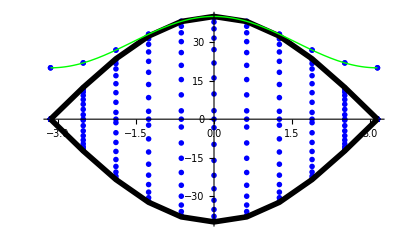

```mathematica
twoExcitonSpectrum=ListPlot[spectrumList2,PlotStyle-> pointstyle2,PlotRange-> All];
p4=ListPlot[{eminfree2,emaxfree2},Joined-> True,PlotStyle-> {{Black,Thickness[0.01]},{Black,Thickness[0.01]}}];
p5=Plot[eVektaris[x],{x,-Pi,Pi},PlotStyle-> {Green}];
Print["Green curve is Vektaris' analytical result"]
Show[twoExcitonSpectrum,p4,p5]
(*Show[twoExcitonSpectrum,p4]*)
```

## Three-exciton system

The Schrodiner-like equation for three-exciton system in k representation is 

[ϵ_exciton(k1)+ ϵ_exciton(k2)+ ϵ_exciton(k3)-ϵ_trimer]c(k1,k2,k3)+ 1/N∑_q [c(k1-q,k2+q,k3)+c(k1-q,k2,k3+q)+c(k1,k2-q,k3+q)]D(q)

=2/N∑_q [J(k1-q)c(k1-q,k2+q,k3)+J(k2-q)c(k1,k2-q,k3+q)+J(k3-q)c(k1+q,k2+q,k3-q)]

Before solving this equation, we convert it into an eigenvalue problem
H|ψ_n⟩=E_n|ψ_n⟩

∑_(k1', k2', k3') A_(k1 k2 k3, k1' k2' k3') c(k1', k2', k3')
=ϵ_trimer c(k1,k2,k3)

where
A_(k1 k2 k3, k1' k2' k3')
=δ_(k1',k1)δ_(k2',k2)δ_(k3',k3)[ϵ(k1)+ ϵ(k2)+ ϵ(k3)]+
1/N{δ_(k1',k1)[D(k2-k2')-2J(k2')]+
δ_(k2',k2)[D(k3-k3')-2J(k3')]+
δ_(k3',k3)[D(k1-k1')-2J(k1')]
}

However, this is not the whole story. Because we have assumed that C_(n1, n2, n3)= 0 when any two of {n1, n2, n3} are equal, we have to take into account of that assumption when we are solving the eigenvalue problem.

Let's derive what is the constraint on C(k1, k2, k3)

if k1 + k2 + k3 = K
∑_k1 ∑_k2 C(k1,k2,k3)

=∑_k1 ∑_k2 ∑_n1 ∑_n2 ∑_n3 1/(√N)^3 e^(i(k1 n1 + k2 n2 + k3 n3))C_(n1,n2,n3)
=∑_k1 ∑_k2 ∑_n1 ∑_n2 ∑_n3 1/(√N)^3 e^(ik1(n1-n3))e^(ik2(n2-n3))e^(iK n3) C_(n1,n2,n3)
=√N∑_n1 ∑_n2 ∑_n3 δ_(n1,n3)δ_(n2,n3)e^(iK n3) C_(n1,n2,n3)
=√N∑_n3 e^(iK n3)C_(n3,n3,n3)
=0

Then,the constraint on C(k1,k2,k3)is
 
∑_(k1+k2+k3=K) C(k1,k2,k3)=0

The above constraint will hardly help us. Judging from the apperance of C_(n3, n3, n3), we know that there may exist some other more restricted conditions which correspond to C_(n, n, m), C_(n, m, n) and C_(m, n, n).

if k1 + k2 + k3 = K, and we fix the value of k3
∑_(k1+k2=K-k3) C(k1,k2,k3)

=∑_k1 ∑_n1 ∑_n2 ∑_n3 1/(√N)^3 e^(i(k1 n1 + k2 n2 + k3 n3))C_(n1,n2,n3)
=∑_k1 ∑_n1 ∑_n2 ∑_n3 1/(√N)^3 e^(ik1 n1)e^(i(K-k3-k1)n2)e^(ik3 n3) C_(n1,n2,n3)

=1/(√N)∑_n1 ∑_n2 ∑_n3 (1/N∑_k1 e^(ik1(n1-n2)))e^(i(K-k3)n2)e^(iK n3) C_(n1,n2,n3)

=1/(√N)∑_n1 ∑_n2 ∑_n3 δ_(n1,n2)e^(i(K-k3)n2)e^(iK n3) C_(n1,n2,n3)
=1/(√N)∑_n2 ∑_n3 e^(i(K-k3)n2)e^(iK n3) C_(n2,n2,n3)
=0

The above derivations show that

if {k1, k2, k3} are fixed
∑_(k1'+k2'=K-k3) δ_(k3,k3')C(k1',k2',k3')=0

because when k3'≠ k3, δ_(k3,k3')=0
when k3'=k3, δ_(k3,k3')=1 and ∑_(k1'+k2'=K-k3) C(k1',k2',k3')=0

In summary, we have to solve 

∑_(k1', k2', k3') A_(k1 k2 k3, k1' k2' k3') c(k1', k2', k3')
=ϵ_trimer c(k1,k2,k3)

under the condition that

∑_k1 ∑_(k2=K-k1-k3) C(k1,k2,k3)=0

The matrix A is also not symmetric, but we can do the same thing (just like what we did in the biexciton case) to make it symmetric .
  
 Because
 ∑_(k1'+k2'=K-k3) δ_(k3,k3')C(k1',k2',k3')=0
 
 Add some zeros to the eigen equations, we can obtain

∑_(k1', k2', k3') A_(k1 k2 k3, k1' k2' k3') c(k1', k2', k3') + 

1/N∑_(k1', k2', k3') {
δ_(k1',k1)[-2J(k2)]×c(k1', k2', k3') +
δ_(k2',k2)[-2J(k3)]×c(k1', k2', k3')+
δ_(k3',k3)[-2J(k1)]×c(k1', k2', k3')}

=ϵ_trimer c(k1,k2,k3)

(the red is the original equation, the black part is 0)

Then the new symmetric matrix B is

B_(k1 k2 k3, k1' k2' k3')
=δ_(k1',k1)δ_(k2',k2)δ_(k3',k3)[ϵ(k1)+ ϵ(k2)+ ϵ(k3)]+
1/N{δ_(k1',k1)[D(k2-k2')-2J(k2')-2J(k2)]
+
δ_(k2',k2)[D(k3-k3')-2J(k3')-2J(k3)]
+
δ_(k3',k3)[D(k1-k1')-2J(k1')-2J(k1)]
}

==============================
ignore the equations below
∑_(k1', k2', k3')^(exclude{q1,q2,q3}) A_(k1 k2 k3, k1' k2' k3')×
c(k1',k2',k3') + A_(k1 k2 k3, q1 q2 q3)c(q1,q2,q3)

=∑_(k1', k2', k3')^(exclude{q1,q2,q3}) A_(k1 k2 k3, k1' k2' k3')×
c(k1',k2',k3') + A_(k1 k2 k3, q1 q2 q3)(-∑_(k1', k2', k3')^(exclude{q1,q2,q3}) c(k1',k2',k3'))

=∑_(k1', k2', k3')^(exclude{q1,q2,q3}) (A_(k1 k2 k3, k1' k2' k3')-A_(k1 k2 k3, q1 q2 q3))×c(k1',k2',k3') 

=E c(k1',k2',k3')

```mathematica
(* generate a array of a list like this {{i1,j1,k1},{i2,j2,k2},... } *)
trimers=Flatten[
Table[{i,j,k},{i,-Nmol/2+1,Nmol/2},{j,-Nmol/2+1,Nmol/2},{k,-Nmol/2+1,Nmol/2}],
2
];
```

```mathematica
select[trimers_,ktotal_]:=Module[{a},
(* ktotal is from -Nmol/2 to Nmol/2 *)

(* check the trimer {i,j,k}: if i+j+k = ktotal + Integer*Nmol, give 1, otherwise 0 *)
check[list_]:=If[
Mod[Apply[Plus,list]-ktotal,Nmol]==0,1,
0
];

a=Map[check,trimers]
(* the above step will give a list of 0 and 1,
1 means that the corresponding {i,j,k} satisfy that i+j+k is equivalent to ktotal and is required for the expansion of the hamiltonian, 0 means it is not needed  *)
]

(* counting how many 1's in list x *)
counting[x_]:=Count[x,1]
```

```mathematica
a=select[trimers,0];
ndim=counting[a]
index=Flatten[Position[a,1]];
selectedTrimers=Part[trimers,index];
```

400

```mathematica
(* fixed the first index k1 *)
pick1index[list_]:=Table[
Flatten[
Position[list,List[k1,_,_]]
],
{k1,-Nmol/2+1,Nmol/2}
]

(* fixed the second index k2 *)
pick2index[list_]:=Table[
Flatten[
Position[list,List[_,k2,_]]
],
{k2,-Nmol/2+1,Nmol/2}
]

(* fixed the third index k3 *)
pick3index[list_]:=Table[
Flatten[
Position[list,List[_,_,k3]]
],
{k3,-Nmol/2+1,Nmol/2}
]
```

```mathematica
(*Print["ktotal        number of states"]
Do[ilist=select[trimers,i];Print[{i,counting[ilist]}],{i,-Nmol/2,Nmol/2-1}]*)
```

```mathematica
(* calculate off-diagonal elements *)
offdiag[trimer1_List,trimer2_List]:=Module[
{k1a,k2a,k3a,k1b,k2b,k3b,difference,whereisZero,len},

difference=trimer1-trimer2;
whereisZero=Flatten[Position[difference,0]];
len=Length[whereisZero];
{k1a,k2a,k3a}=trimer1;
{k1b,k2b,k3b}=trimer2;

Which[
(* no k are equal for two trimers*)
len==0,0.0,

(* all k's are equal for two trimers*)
len==3,
(Dk[k2a-k2b]-2Jk[k2b]-2Jk[k2a]+Dk[k3a-k3b]-2Jk[k3b]-2Jk[k3a]+
Dk[k1a-k1b]-2Jk[k1b]-2Jk[k1a])/Nmol,

(* only one k are equal for two trimers*)
 (len==1)&&(whereisZero⟦1⟧==1)(*&&(Mod[k2a+k3a-k2b-k3b,Nmol]==0)*),(Dk[k2a-k2b]-2Jk[k2b]-2Jk[k2a])/Nmol,

 (len==1)&&(whereisZero⟦1⟧==2)(*&&(Mod[k1a+k3a-k1b-k3b,Nmol]==0)*),(Dk[k3a-k3b]-2Jk[k3b]-2Jk[k3a])/Nmol,

 (len==1)&&(whereisZero⟦1⟧==3)(*&&(Mod[k1a+k2a-k1b-k2b,Nmol]==0)*),(Dk[k1a-k1b]-2Jk[k1b]-2Jk[k1a])/Nmol
]
]
```

```mathematica
emaxfree={};
eminfree={};
(*h={};*)
```

```mathematica
efimov[totalK_]:=Module[
{a,ndim,selectedTrimers,diag,ham,emax,emin,eigVal,ka,energy,vectors,onevector,coeff1,coeff2,coeff3,sum1,sum2,sum3,test1,test2,test3,deleteIndex},
deleteIndex={};
(* find the trimers whose total vector is equal to totalK *)
a=select[trimers,totalK];
(* a is a list of 0's and 1's *)
ndim=counting[a];
index=Flatten[Position[a,1]];
(* select trimers whose wavevectors add up to totalK *)
selectedTrimers=Part[trimers,index];
    diag=Map[diagonalpart,selectedTrimers];
emax=Max[diag];
emin = Min[diag];
ham = DiagonalMatrix[diag];

(* calculate the off-diagonal elements *)
Do[
ham⟦i,j⟧=ham⟦i,j⟧+offdiag[selectedTrimers⟦i⟧,selectedTrimers⟦j⟧];
ham⟦j,i⟧=ham⟦i,j⟧,
{i,1,Length[selectedTrimers]},
{j,i,Length[selectedTrimers]}
];
(*h=ham;*)
(*eigVal=Eigenvalues[ham];*)

ka=N[totalK*2*Pi/Nmol];
emaxfree=Append[emaxfree,{ka,emax}];
eminfree=Append[eminfree,{ka,emin}];
{energy,vectors}=Eigensystem[ham];

(* filtering eigenvalues based on eigenvectors *)
Do[
(* fixed the first index k1 *)
onevector=vectors⟦i⟧;
coeff1=Map[
Part[onevector,#]&,pick1index[selectedTrimers]
];
sum1=Apply[Plus,coeff1,2];
test1=Map[(#< 10^-10)&,sum1];
(* fixed the second index k2 *)
coeff2=Map[
Part[onevector,#]&,pick2index[selectedTrimers]
];
sum2=Apply[Plus,coeff2,2];
test2=Map[(#< 10^-10)&,sum2];
(* fixed the second index k3 *)
coeff3=Map[
Part[onevector,#]&,pick3index[selectedTrimers]
];
sum3=Apply[Plus,coeff3,2];
test3=Map[(#< 10^-10)&,sum3];
If[
Apply[And,Join[test1,test2,test3]]==False,
deleteIndex=Append[deleteIndex,{i}]
],
{i,1,Length[vectors]}
];
(*deleteIndex=Position[selected,False];*)
eigVal=Delete[energy,deleteIndex];
Table[{ka,eigVal⟦i⟧},{i,1,Length[eigVal]}]
]
```

```mathematica
deleteIndex={};
```

```mathematica
efimov[0]
```

{{0.,60.},{0.,57.8327},{0.,53.5212},{0.,53.5212},{0.,51.5656},{0.,45.7659},{0.,45.7659},{0.,41.8779},{0.,36.6006},{0.,36.6006},{0.,34.7156},{0.,34.7156},{0.,29.8194},{0.,-27.4658},{0.,-27.4658},{0.,26.3874},{0.,26.3874},{0.,-24.1418},{0.,-24.1418},{0.,-23.4497},{0.,-23.4497},{0.,-22.2154},{0.,-22.2154},{0.,22.0856},{0.,22.0856},{0.,-19.4545},{0.,-18.6035},{0.,-18.6035},{0.,-18.4276},{0.,-18.1513},{0.,-18.1513},{0.,-17.9443},{0.,-17.9443},{0.,16.6968},{0.,16.5334},{0.,16.5334},{0.,-15.179},{0.,-12.4048},{0.,-12.4048},{0.,12.0875},{0.,12.0875},{0.,-10.466},{0.,-10.466},{0.,-9.46152},{0.,-9.46152},{0.,9.10477},{0.,9.10477},{0.,8.11078},{0.,8.11078},{0.,-7.09126},{0.,3.93218},{0.,-2.82264},{0.,-2.82264},{0.,2.21393},{0.,2.21393},{0.,-6.3558×10^-14},{0.,-9.08376×10^-15},{0.,6.08003×10^-15}}

```mathematica
(*Do[Print[i," ",j," ", h⟦i,j⟧," ", h⟦j,i⟧],{i,1,ndim-1},{j,i+1,ndim}]*)
```

```mathematica
eminfree={};
emaxfree={};
Do[spectrum[i]=efimov[i];Print[Length[spectrum[i]]],{i,-Nmol/2,Nmol/2}];
spectrumList=Table[spectrum[i],{i,-Nmol/2,Nmol/2}];
pointstyle1=Table[{Red,PointSize[0.01]},{i,-Nmol/2,Nmol/2}];
```

48

57

57

57

«5 more identical outputs»

58

58

57

57

57

«6 more identical outputs»

48

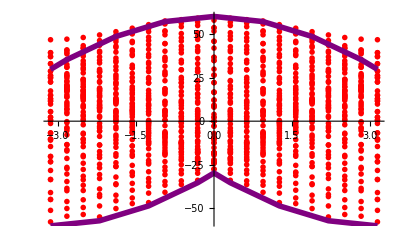

```mathematica
threeExcitonSpecturm=ListPlot[spectrumList,PlotStyle-> pointstyle1];

threeExcitonFree=ListPlot[{eminfree,emaxfree},Joined-> True,PlotStyle-> {{Purple,Thickness[0.01]},{Purple,Thickness[0.01]}}];
Show[threeExcitonSpecturm,threeExcitonFree]
```

```mathematica
Export["/home/krems/pxiang/trimer/threeExcitonSpectrum.dat",Flatten[spectrumList,1]]
Export["/home/krems/pxiang/trimer/threeFreeExcitonEmax.dat",emaxfree]
Export["/home/krems/pxiang/trimer/threeFreeExcitonEmin.dat",eminfree]
```

/home/krems/pxiang/trimer/threeExcitonSpectrum.dat

/home/krems/pxiang/trimer/threeFreeExcitonEmax.dat

/home/krems/pxiang/trimer/threeFreeExcitonEmin.dat

```mathematica
ktotal = 0;
```

```mathematica
all=
Table[ 
If[
Mod[kb + k - ktotal,Nmol]==0,
{kb*2Pi/Nmol,k*2 Pi/Nmol},
None],
{kb,-Nmol/2+1,Nmol/2},
{k,-Nmol/2+1,Nmol/2}
]
```

{{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(9 π)/10,(9 π)/10},None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(4 π)/5,(4 π)/5},None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(7 π)/10,(7 π)/10},None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(3 π)/5,(3 π)/5},None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-π/2,π/2},None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,{-(2 π)/5,(2 π)/5},None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,{-(3 π)/10,(3 π)/10},None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,{-π/5,π/5},None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,{-π/10,π/10},None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,{0,0},None,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,{π/10,-π/10},None,None,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,{π/5,-π/5},None,None,None,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,{(3 π)/10,-(3 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,{(2 π)/5,-(2 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None},{None,None,None,None,{π/2,-π/2},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None},{None,None,None,{(3 π)/5,-(3 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None},{None,None,{(7 π)/10,-(7 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None},{None,{(4 π)/5,-(4 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None},{{(9 π)/10,-(9 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{π,π}}}

```mathematica
all=Flatten[all,1]
```

{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(9 π)/10,(9 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(4 π)/5,(4 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(7 π)/10,(7 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(3 π)/5,(3 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-π/2,π/2},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(2 π)/5,(2 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-(3 π)/10,(3 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-π/5,π/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{-π/10,π/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{0,0},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{π/10,-π/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{π/5,-π/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(3 π)/10,-(3 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(2 π)/5,-(2 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{π/2,-π/2},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(3 π)/5,-(3 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(7 π)/10,-(7 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(4 π)/5,-(4 π)/5},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{(9 π)/10,-(9 π)/10},None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,{π,π}}

```mathematica
selected = Cases[all,Except[None]]
```

{{-(9 π)/10,(9 π)/10},{-(4 π)/5,(4 π)/5},{-(7 π)/10,(7 π)/10},{-(3 π)/5,(3 π)/5},{-π/2,π/2},{-(2 π)/5,(2 π)/5},{-(3 π)/10,(3 π)/10},{-π/5,π/5},{-π/10,π/10},{0,0},{π/10,-π/10},{π/5,-π/5},{(3 π)/10,-(3 π)/10},{(2 π)/5,-(2 π)/5},{π/2,-π/2},{(3 π)/5,-(3 π)/5},{(7 π)/10,-(7 π)/10},{(4 π)/5,-(4 π)/5},{(9 π)/10,-(9 π)/10},{π,π}}

```mathematica
energyList = N[eVektaris[#⟦1⟧]+2 propagate Cos[#⟦2⟧]]&/@ selected
```

{1.4683,5.72949,12.3664,20.7295,30.,39.2705,47.6336,54.2705,58.5317,60.,58.5317,54.2705,47.6336,39.2705,30.,20.7295,12.3664,5.72949,1.4683,0.}

{{{-π,40.},{-π,20.}},{{-(9 π)/10,40.931},{-(9 π)/10,19.069}},{{-(4 π)/5,43.1433},{-(4 π)/5,16.8567}},{{-(7 π)/10,46.1803},{-(7 π)/10,13.8197}},{{-(3 π)/5,49.2705},{-(3 π)/5,10.7295}},{{-π/2,52.1113},{-π/2,7.8887}},{{-(2 π)/5,54.899},{-(2 π)/5,5.10102}},{{-(3 π)/10,57.1113},{-(3 π)/10,2.8887}},{{-π/5,58.5317},{-π/5,1.4683}},{{-π/10,59.5106},{-π/10,0.489435}},{{0,60.},{0,0.}},{{π/10,59.5106},{π/10,0.489435}},{{π/5,58.5317},{π/5,1.4683}},{{(3 π)/10,57.1113},{(3 π)/10,2.8887}},{{(2 π)/5,54.899},{(2 π)/5,5.10102}},{{π/2,52.1113},{π/2,7.8887}},{{(3 π)/5,49.2705},{(3 π)/5,10.7295}},{{(7 π)/10,46.1803},{(7 π)/10,13.8197}},{{(4 π)/5,43.1433},{(4 π)/5,16.8567}},{{(9 π)/10,40.931},{(9 π)/10,19.069}},{{π,40.},{π,20.}}}

{{{-π,40.},{-(9 π)/10,40.931},{-(4 π)/5,43.1433},{-(7 π)/10,46.1803},{-(3 π)/5,49.2705},{-π/2,52.1113},{-(2 π)/5,54.899},{-(3 π)/10,57.1113},{-π/5,58.5317},{-π/10,59.5106},{0,60.},{π/10,59.5106},{π/5,58.5317},{(3 π)/10,57.1113},{(2 π)/5,54.899},{π/2,52.1113},{(3 π)/5,49.2705},{(7 π)/10,46.1803},{(4 π)/5,43.1433},{(9 π)/10,40.931},{π,40.}},{{-π,20.},{-(9 π)/10,19.069},{-(4 π)/5,16.8567},{-(7 π)/10,13.8197},{-(3 π)/5,10.7295},{-π/2,7.8887},{-(2 π)/5,5.10102},{-(3 π)/10,2.8887},{-π/5,1.4683},{-π/10,0.489435},{0,0.},{π/10,0.489435},{π/5,1.4683},{(3 π)/10,2.8887},{(2 π)/5,5.10102},{π/2,7.8887},{(3 π)/5,10.7295},{(7 π)/10,13.8197},{(4 π)/5,16.8567},{(9 π)/10,19.069},{π,20.}}}

{{-3.14159,40.},{-2.82743,40.931},{-2.51327,43.1433},{-2.19911,46.1803},{-1.88496,49.2705},{-1.5708,52.1113},{-1.25664,54.899},{-0.942478,57.1113},{-0.628319,58.5317},{-0.314159,59.5106},{0.,60.},{0.314159,59.5106},{0.628319,58.5317},{0.942478,57.1113},{1.25664,54.899},{1.5708,52.1113},{1.88496,49.2705},{2.19911,46.1803},{2.51327,43.1433},{2.82743,40.931},{3.14159,40.}}

/home/krems/pxiang/trimer/biexcitonPlusExcitonEmax.dat

{{-3.14159,20.},{-2.82743,19.069},{-2.51327,16.8567},{-2.19911,13.8197},{-1.88496,10.7295},{-1.5708,7.8887},{-1.25664,5.10102},{-0.942478,2.8887},{-0.628319,1.4683},{-0.314159,0.489435},{0.,0.},{0.314159,0.489435},{0.628319,1.4683},{0.942478,2.8887},{1.25664,5.10102},{1.5708,7.8887},{1.88496,10.7295},{2.19911,13.8197},{2.51327,16.8567},{2.82743,19.069},{3.14159,20.}}

/home/krems/pxiang/trimer/biexcitonPlusExcitonEmin.dat

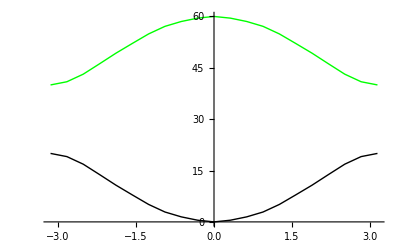

```mathematica
biexcitonPlusFreeExciton[ktotal_] :=Module[ 
{all,selected,energyList,ka,emax,emin},
all=Table[ 
If[
Mod[kb + k - ktotal,Nmol]==0,
{kb*2Pi/Nmol,k*2 Pi/Nmol},
None],
{kb,-Nmol/2+1,Nmol/2},
{k,-Nmol/2+1,Nmol/2}
];
all=Flatten[all,1];
selected = Cases[all,Except[None]];
energyList = N[eVektaris[#⟦1⟧]+2 propagate Cos[#⟦2⟧]]&/@ selected;
ka = ktotal*2*Pi/Nmol;
emax = Max[energyList];
emin = Min[energyList];
{{ka,emax},{ka,emin}}
]
bpf = biexcitonPlusFreeExciton[#]& /@ Table[i,{i,-Nmol/2,Nmol/2}]
maxAndmin=MapThread[List,bpf,1]
max=maxAndmin[[1]]//N
Export["/home/krems/pxiang/trimer/biexcitonPlusExcitonEmax.dat",max]
min = maxAndmin[[2]]//N
Export["/home/krems/pxiang/trimer/biexcitonPlusExcitonEmin.dat",min]
biexcitonPlusFree=ListLinePlot[maxAndmin,PlotStyle-> {Green,Black}]
(*biexcitonPlusFree=ListLinePlot[bpf,PlotStyle-> {Green}]*)
```

Red dots represent all the eigenenergies of three-exciton system

Green are the maximum energies of biexciton + one free exciton

Black are the maximum energies of biexciton + one free exciton

Purple represent the boundaries of three-exciton continuum

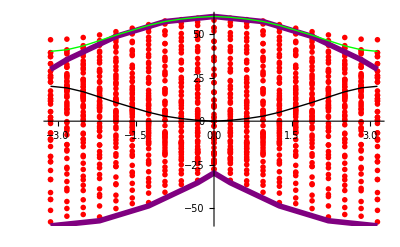

```mathematica
Print["Red dots represent all the eigenenergies of three-exciton system"]
Print["Green are the maximum energies of biexciton + one free exciton"]
Print["Black are the maximum energies of biexciton + one free exciton"]
Print["Purple represent the boundaries of three-exciton continuum"]
Show[threeExcitonSpecturm,threeExcitonFree,biexcitonPlusFree]
```